# Zestaw 9

## Zadanie 1. Wybrane operacje na macierzach, Determinant, Trace, Transpose, Inverse, CharacteristicPolynomial, Eigensystem

Zdefiniuj macierz 𝐌:

```mathematica
M = { {a, b}, {c, d} };

 MatrixForm @ M
```

(a | b
c | d)

Wykonaj następujące operacje:

#### 1)

```mathematica
Det[M]
```

-b c+a d

#### 2)

```mathematica
Tr[M]
```

a+d

#### 3)

```mathematica
MatrixForm @ Transpose[M]
```

(a | c
b | d)

#### 4)

```mathematica
MatrixForm[M . M]
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

#### 5)

```mathematica
MatrixForm[M * M]
```

(a^2 | b^2
c^2 | d^2)

#### 6)

```mathematica
MInverse = Inverse[M];
MatrixForm[MInverse]
```

(d/(-b c+a d) | -b/(-b c+a d)
-c/(-b c+a d) | a/(-b c+a d))

#### 7)

```mathematica
Id = Simplify[M . MInverse];
MatrixForm[Id]
```

(1 | 0
0 | 1)

#### 8)

```mathematica
CharacteristicPolynomial[M, λ]
```

-b c+a d-a λ-d λ+λ^2

#### 9)

```mathematica
val1 = Simplify @ Det[M - λ Id]
```

-b c+(a-λ) (d-λ)

```mathematica
val2 = Simplify[λ^2 - λ Tr[M] + Det[M]]
```

-b c+(a-λ) (d-λ)

```mathematica
val1 === val2
```

True

#### 10) znajdź wartości własne i odpowiadające im wektory własne

```mathematica
{{λ1, λ2}, {v1, v2}} = Eigensystem[M]
```

{{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))},{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),1},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c),1}}}

```mathematica
Eigenvalues[M] == {λ1, λ2}
```

True

```mathematica
Eigenvectors[M] == {v1, v2}
```

True

### Następnie zweryfikuj, że odpowiadają wartościom własnym , które są miejscami zerowymi wielomianu charakterystycznego.

```mathematica
λ1
λ2
```

1/2 (a+d-√(a^2+4 b c-2 a d+d^2))

1/2 (a+d+√(a^2+4 b c-2 a d+d^2))

```mathematica
λminus= Simplify @ (Tr[M] - Sqrt[ Tr[M]^2 - 4 Det[M] ]) / 2 

λplus= Simplify @ (Tr[M] + Sqrt[ Tr[M]^2 - 4 Det[M] ]) / 2
```

1/2 (a+d-√(a^2+4 b c-2 a d+d^2))

1/2 (a+d+√(a^2+4 b c-2 a d+d^2))

```mathematica
λ1 === λminus
λ2 === λplus
```

True

True

### Dalej, utwórz macierz , której kolumnami są odpowiednie wektory własne

Uważaj na konwencje w Mathematica®, może być konieczne użycie Transpose.

```mathematica
v1 = FullSimplify[v1]
v2 = FullSimplify[v2]
```

{-(-a+√(4 b c+(a-d)^2)+d)/(2 c),1}

{(a+√(4 b c+(a-d)^2)-d)/(2 c),1}

```mathematica
B = Transpose[{v1, v2}];
MatrixForm[B]
```

(-(-a+√(4 b c+(a-d)^2)+d)/(2 c) | (a+√(4 b c+(a-d)^2)-d)/(2 c)
1 | 1)

### Zweryfikuj

```mathematica
leftSide = FullSimplify[Inverse[B] . M . B];
MatrixForm[leftSide]
```

(1/2 (a-√(4 b c+(a-d)^2)+d) | 0
0 | 1/2 (a+√(4 b c+(a-d)^2)+d))

```mathematica
rightSide = FullSimplify @ {
{λ1, 0},
{0, λ2} 
};
MatrixForm[rightSide]
```

(1/2 (a-√(4 b c+(a-d)^2)+d) | 0
0 | 1/2 (a+√(4 b c+(a-d)^2)+d))

```mathematica
leftSide === rightSide
```

True

### Znając oraz wartości własne oblicz -tą potęgę macierzy .

```mathematica
BToPower[k_] := FullSimplify[
B . {
{λ1^k,         0},
{        0, λ2^k} 
} . Inverse[B]
]
MatrixForm @ BToPower[k]
```

((2^(-1-k) ((a-√(4 b c+(a-d)^2)+d)^k (-a+√(4 b c+(a-d)^2)+d)+(a+√(4 b c+(a-d)^2)-d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)) | (2^-k b (-(a-√(4 b c+(a-d)^2)+d)^k+(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2))
(2^-k c (-(a-√(4 b c+(a-d)^2)+d)^k+(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)) | (2^(-1-k) ((a+√(4 b c+(a-d)^2)-d) (a-√(4 b c+(a-d)^2)+d)^k+(-a+√(4 b c+(a-d)^2)+d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)))

Porównaj z wynikiem funkcji MatrixPower[M, k].

```mathematica
BToKBuildInResult = FullSimplify[MatrixPower[M, k]];
MatrixForm @ BToKBuildInResult
```

((2^(-1-k) ((a-√(4 b c+(a-d)^2)+d)^k (-a+√(4 b c+(a-d)^2)+d)+(a+√(4 b c+(a-d)^2)-d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)) | (2^-k b (-(a-√(4 b c+(a-d)^2)+d)^k+(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2))
(2^-k c (-(a-√(4 b c+(a-d)^2)+d)^k+(a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)) | (2^(-1-k) ((a+√(4 b c+(a-d)^2)-d) (a-√(4 b c+(a-d)^2)+d)^k+(-a+√(4 b c+(a-d)^2)+d) (a+√(4 b c+(a-d)^2)+d)^k))/(√(4 b c+(a-d)^2)))

```mathematica
BToPower[k] === BToKBuildInResult
```

True

## Zadanie 2. Macierz przejścia dla łańcucha Markowa, DiscreteMarkovProcess, Graph, EdgeLabels, Transpose, Eigensystem

Rozważmy układ fizyczny, np. cząstkę przeskakującą między trzema komorami detektora, który może znajdować się w jednym z trzech stanów: {1, 2, 3}.

Dynamikę układu opisuje macierz przejścia  :

```mathematica
P = {
{ 1/3,   0,          2/3},
{ 1/10, 9/10, 0      },
{ 1/3,   0,          2/3}
};
MatrixForm[P]
```

(1/3 | 0 | 2/3
1/10 | 9/10 | 0
1/3 | 0 | 2/3)

W celu zbadania własności łańcucha Markowa wykonaj następujące polecenia:

### 1) Sprawdź, czy macierz jest poprawną macierzą stochastyczną

Co to oznacza? Jaka powinna być suma prawdopodobieństw w każdym wierszu?
Odp.: Macierz stochastyczna - macierz kwadratowa o nieujemnych współczynnikach, której każdy z wierszy sumuje się do 1.

```mathematica
Total @ Transpose[P]
```

{1,1,1}

### 2) Jaka jest interpretacja kolumn oraz sumy elementów w kolumnach macierzy

Odp.: -ta kolumna - Po podzieleniu przez liczbę wierszy/kolumn jest to prawdopodobieństwo zajścia przejścia z danego stanu (indeks wiersza) do stanu .
Suma elementów w -tej kolumnie - Po podzieleniu przez liczbę wierszy/kolumn jest to prawdopodobieństwo, że po przejściu znajdziemy się w stanie .

### 3) Przedstaw macierz jako graf, na którym wierzchołki odpowiadają stanom, a krawędzie są opisane wartościami prawdopodobieństw przejść

Najpierw zdefiniuj łańcuch Markowa korzystając z DiscreteMarkovProcess, a następnie skorzystaj z Graph oraz EdgeLabels.

```mathematica
?DiscreteMarkovProcess
```

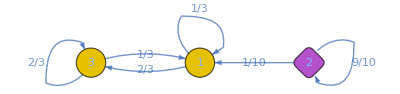

```mathematica
process = DiscreteMarkovProcess[1, P];

edgeLabels = Select [
element |-> Last[element] > 0
][Flatten @ Table[
i -> j -> P[[i, j]],
{i, 3}, {j, 3}
]];

Graph[process, EdgeLabels->edgeLabels]
```

Alternatywnie można skorzystać z WeightedAdjacencyGraph dla macierzy .

### 4) Oblicz , oraz

```mathematica
PToPower[n_] := MatrixForm @ MatrixPower[N[P], n]
```

```mathematica
PToPower[2]
```

(0.333333 | 0. | 0.666667
0.123333 | 0.81 | 0.0666667
0.333333 | 0. | 0.666667)

```mathematica
PToPower[5]
```

(0.333333 | 0. | 0.666667
0.180243 | 0.59049 | 0.229267
0.333333 | 0. | 0.666667)

```mathematica
PToPower[100]
```

(0.333333 | 0. | 0.666667
0.333326 | 0.0000265614 | 0.666647
0.333333 | 0. | 0.666667)

Jaka jest fizyczna interpretacja elementu  macierzy ?
Odp.: Prawdopodobieństwo zajścia przejścia ze stanu i do stanu j po n krokach.

### 5) Oblicz granicę

```mathematica
Pinf = Limit[MatrixPower[P, k], k -> Infinity];
MatrixForm @ Pinf
```

(1/3 | 0 | 2/3
1/3 | 0 | 2/3
1/3 | 0 | 2/3)

### 6) Znajdź analitycznie rozkład stacjonarny , rozwiązując układ równań przy warunku normalizacji

```mathematica
pi= {π1, π2, π3};

piSolved1 = Flatten @ Solve[pi . P == pi && Total[pi] == 1, pi]
```

{π1→1/3,π2→0,π3→2/3}

### 7) Rozwiąż problem z 6) znajdując odpowiednie wartości własne i wektory własne macierzy

Użyj Eigensystem. Zwróć uwagę na to, czy Mathematica® liczy wektory prawostronne czy lewostronne.
W razie konieczności użyj macierzy transponowanej .

```mathematica
{vals,vecs}=Eigensystem[Transpose[P]];
rawPi=vecs[[1]];

piSolved2=rawPi/Total[rawPi]
```

{1/3,0,2/3}

Zidentyfikuj, który wektor własny odpowiada rozkładowi stacjonarnemu i dlaczego.
Odp.: Rozkładowi stacjonarnemu odpowiada ten wektor własny, który jest przypisany do wartości własnej .

### 8) Porównaj wyniki z 5), 6) oraz 7)

```mathematica
resultTask5 = Total[Pinf] / Total @ Flatten[Pinf]
```

{1/3,0,2/3}

```mathematica
resultTask6 = Map[
entry |-> Last[entry],
piSolved1
]
```

{1/3,0,2/3}

```mathematica
resultTask7 = piSolved2
```

{1/3,0,2/3}

```mathematica
resultTask5 === resultTask6 && resultTask6 === resultTask7
```

True

## Zadanie 3. Teoria macierzy losowych a poziomy energetyczne Hamiltonianu, RandomVariate, NormalDistribution, Diagonal, Eigenvalues

Sprawdź przewidywania Wignera. W tym celu:

### 1) Wygeneruj dużą macierz losową o wymiarach dla , której elementy są liczbami rzeczywistymi wylosowanymi z rozkładu normalnego

Użyj RandomVariate oraz NormalDistribution

```mathematica
n = 2000;
H = RandomVariate[
NormalDistribution[],
{n, n}
];

Dimensions[H]
```

{2000,2000}

```mathematica
MatrixForm @ H[[;;4, ;;4]]
```

(1.22824 | -1.47567 | -0.502317 | -0.0805919
-0.60846 | 1.60274 | -1.54581 | 0.733469
-1.37909 | 1.99696 | 1.4094 | -0.307936
-1.57763 | -1.74548 | -0.228774 | 0.975245)

### 2) Sprawdź odchylenie standardowe elementów macierzy

```mathematica
StandardDeviation @ Flatten[H]
```

1.00033

### 3) Zsymetryzuj macierz by uzyskać hamiltonian

```mathematica
HSym = (H + Transpose[H]) / 2;
MatrixForm @ HSym[[;;4, ;;4]]
```

(1.22824 | -1.04206 | -0.940701 | -0.829109
-1.04206 | 1.60274 | 0.225573 | -0.506005
-0.940701 | 0.225573 | 1.4094 | -0.268355
-0.829109 | -0.506005 | -0.268355 | 0.975245)

### 4) Sprawdź odchylenie standardowe wszystkich elementów macierzy oraz tylko elementów diagonalnych

```mathematica
σ = StandardDeviation @ Flatten[HSym]
```

0.707881

```mathematica
StandardDeviation @ Diagonal[HSym]
```

1.01276

Jak tłumaczysz ten wynik?
Odp.: Centralne Twierdzenie Graniczne:

### 5) Oblicz numerycznie wszystkie wartości własne otrzymanej macierzy

```mathematica
eigenvalues = Eigenvalues[HSym];
eigenvalues[[;;10]]
```

{63.0478,-63.0132,-62.5761,62.386,-62.3296,62.0483,62.0114,-62.0089,-61.8543,-61.6802}

### 6) Stwórz unormowany histogram wartości własnych, tak by przedstawiał funkcję gęstości prawdopodobieństwa

Użyj "PDF" jako opcji w Histogram.

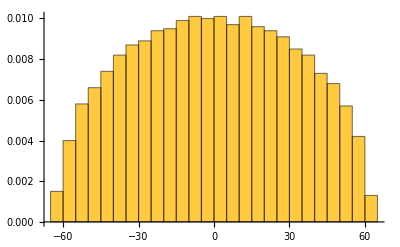

```mathematica
histogram = Histogram[eigenvalues, 30, "PDF"]
```

### 7) Na wykresie z 6) nanieś zależność teoretyczną opisującą półkole Wignera z odpowiednio dobranymi parametrami oraz

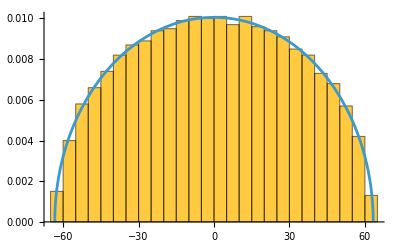

```mathematica
ρ[σ_, N_][E_] := Sqrt[4 N σ^2 - E^2] / (2 π N σ^2 ) 
EMax = 2 σ Sqrt[n];
EMin = -EMax;

Show[
histogram,
Plot[
ρ[σ, n][x],
{x, EMin, EMax}
]
]
```

### 8) Powtórz punkty od 1) do 7), ale tym razem wygeneruj macierz z elementami z rozkładu jednostajnego na przedziale

Użyj UniformDistribution.

```mathematica
HUniform = RandomVariate[
UniformDistribution[],
{n, n}
];

StandardDeviation @ Flatten[HUniform]
```

0.28871

```mathematica
HUniformSym = (HUniform + Transpose[HUniform]) / 2;
σUniform = StandardDeviation @ Flatten[HUniformSym]
```

0.204225

```mathematica
StandardDeviation @ Diagonal[HUniformSym]
```

0.292667

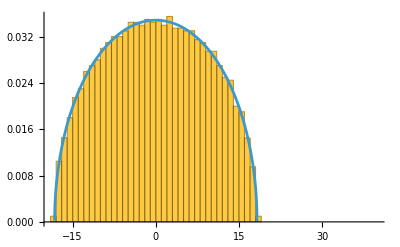

```mathematica
eigenvaluesUniform = Eigenvalues[HUniformSym];
histogramUniform = Histogram[eigenvaluesUniform, 1000, "PDF"];

ρUniform[σ_, N_][E_] := Sqrt[4 N σ^2 - E^2] / (2 π N σ^2 ) 

EMaxUniform = 2 σUniform Sqrt[n];
EMinUniform = -EMax;

Show[
histogramUniform,
Plot[
ρUniform[σUniform, n][x],
{x, EMinUniform, EMaxUniform}
]
]
```

Czy kształt histogramu nadal przypomina półkole?
Odp.: Tak